```mathematica
Mixing (both bound)
```

## DEFINE PARAMTERS

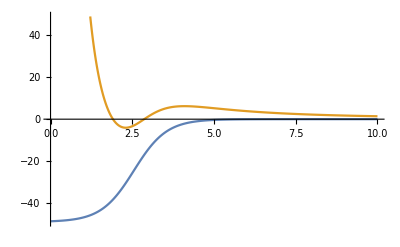

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=49;R=2.55;a=0.5;μ=8/9 Subscript[m, N];
E2=3;
rmax=10.;dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_,l_]:=(l(l+1)ℏc^2)/(2μ r^2);
V00[r_]:=Vwoods[r]+Vcent[r,0];
V22[r_]:=Vwoods[r]+Vcent[r,2];
V00mat=DiagonalMatrix[V00[rlist]];
V22mat=DiagonalMatrix[V22[rlist]];
(*MIXING*)
V02mat=V20mat=DiagonalMatrix[Vwoods[rlist]];
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H000:=V00mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
H022:=V22mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1])+E2;
H0:=ArrayFlatten[{{H000,V02mat},{V20mat,H022}}];
ListLinePlot[{V00[rlist],V22[rlist]},DataRange->{dr,rmax},PlotRange->{-V0,V0}]
```

## SOLUTIONS

```mathematica
(*DEFINITIONS*)
k0[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
k2[En_?NumericQ]:=Sqrt[(2μ (En-E2))/ℏc^2];
wave0[En_,r_]:=SphericalHankelH1[0,k0[En] r];
wave2[En_,r_]:=SphericalHankelH1[2,k2[En] r];
B0[En_]:=rmax/wave0[En,rmax](D[wave0[En,r],r]/.r->rmax);
B2[En_]:=rmax/wave2[En,rmax](D[wave2[En,r],r]/.r->rmax);
(*HAMILTONIAN*)
Hnew[En_]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B0[En]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B2[En]/rmax-1);H];
(*RETURNS EIGENVALUE*)
ϵ=10^-10;
n=2;
evals=List[];evecs=List[];
eigenv[{En_?NumericQ,i_}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En]]],First];{eval[[i]],i});
```

```mathematica
(*RETURNS EIGENSYSTEM*)
En=NestWhileList[eigenv,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];
While[Re[En]<0,
evals=Append[evals,En];
evecs=Append[evecs,evec[[n]]];
n++;
If[Re[eigenv[eigenv[{-V0/2,n}]][[1]]]<0,En=NestWhileList[eigenv,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];,En=1;]]
```

```mathematica
eigenv[{-V0/2,2}]
```

{0.772712+0. ⅈ,2}

```mathematica
eigenv[%]
```

{0.340658-0.28802 ⅈ,2}

```mathematica
eigenv[%]
```

{0.0824329-0.245951 ⅈ,2}

```mathematica
eigenv[%]
```

{0.00485149-0.18281 ⅈ,2}

```mathematica
evals(*V0=77MeV,rmax=10fm,dr=0.01*)
```

{-73.0092+0. ⅈ,-16.8488+0. ⅈ}

```mathematica
evals(*V0=60MeV,rmax=10fm,dr=0.01*)
```

{-50.3657+0. ⅈ,-3.94515+0. ⅈ}

```mathematica
evals(*V0=55MeV,rmax=10fm,dr=0.01*)
```

{-43.9924+0. ⅈ,-1.39979+0. ⅈ}

```mathematica
evals(*V0=52MeV,rmax=10fm,dr=0.01*)
```

{-40.2447+0. ⅈ,-0.349966+0. ⅈ}

```mathematica
evals(*V0=51MeV,rmax=10fm,dr=0.01*)
```

{-39.0093+0. ⅈ}

```mathematica
evals(*V0=10MeV,rmax=10fm,dr=0.01*)
```

{-0.280839+0. ⅈ}

```mathematica
evals;(*V0=9MeV,rmax=10fm,dr=0.01*)(*ABORTED*)
eigenv[eigenv[{-V0/2,1}]]
```

{-0.0634222-0.09976 ⅈ,1}

```mathematica
res(*V0=45MeV,rmax=10fm,dr=0.01*)
```

{{-45/2,2},{1.57772+0. ⅈ,2},{1.04768-0.565992 ⅈ,2},{0.835057-0.612417 ⅈ,2},{0.767087-0.601299 ⅈ,2},{0.746794-0.589044 ⅈ,2},{0.741821-0.582304 ⅈ,2},{0.741121-0.579406 ⅈ,2},{0.741296-0.578358 ⅈ,2},{0.7415-0.578039 ⅈ,2},{0.741611-0.577963 ⅈ,2},{0.741658-0.577954 ⅈ,2},{0.741675-0.577957 ⅈ,2},{0.74168-0.577961 ⅈ,2},{0.741681-0.577963 ⅈ,2},{0.741681-0.577963 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2}}

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
const0[i_]:=evecs[[i,-len-1]]/wave0[evals[[i]],rmax];
const2[i_]:=evecs[[i,-1]]/wave2[evals[[i]],rmax];
rmaxx=20.;
norm0[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[Part[evecs⟦i⟧,1;;len],const0[i] wave0[evals[[i]],Range[rmax+dr,rmaxx,dr]]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]];
norm2[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[Part[evecs⟦i⟧,len+1;;2 len],const2[i] wave2[evals[[i]],Range[rmax+dr,rmaxx,dr]]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]];
```

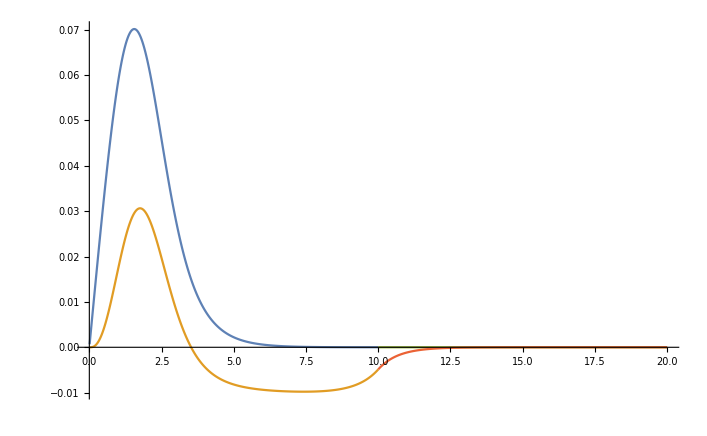

```mathematica
i=1;
ListLinePlot[{Transpose[{rlist,Part[evecs[[i]],1;;len]}],Transpose[{rlist,Part[evecs[[i]],len+1;;2 len]}],Transpose[{Range[rmax,rmaxx,dr], const0[i] wave0[evals[[i]],Range[rmax,rmaxx,dr]]}],Transpose[{Range[rmax,rmaxx,dr], const2[i] wave2[evals[[i]],Range[rmax,rmaxx,dr]]}]},PlotRange->All](*V0=51,rmax=10fm,dr=0.01*)
```

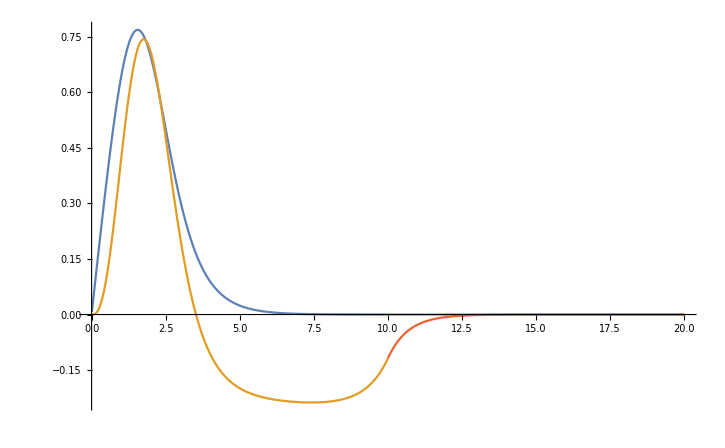

{0.631356-0.529169 ⅈ,2}

```mathematica
i=1;
ListLinePlot[{Transpose[{rlist,norm0[i]Part[evecs[[i]],1;;len]}],Transpose[{rlist,norm2[i] Part[evecs[[i]],len+1;;2 len]}],Transpose[{Range[rmax,rmaxx,dr], norm0[i]const0[i] wave0[evals[[i]],Range[rmax,rmaxx,dr]]}],Transpose[{Range[rmax,rmaxx,dr],norm2[i]const2[i] wave2[evals[[i]],Range[rmax,rmaxx,dr]]}]},PlotRange->All](*V0=51,ramx=10fm,dr=0.01,NORMALISED*)
```